# Discrete Variable Representation

Nirav Mehta

Trinity University

## Introduction

These notes are based on lecture notes of Hans-Dieter Meyer.

These are basic notes serving as a record of my attempt to learn DVR methods.  Numerical methods are broadly divided into so-called "spectral methods" where one chooses an orthonormal basis (e.g. harmonic oscillator states) and calculates matrix elements for a Hamiltonian that can then be diagonalized, and "grid methods" where one uses the position eigenstates as the basis forming a grid.  In grid methods such as the finite-difference method, the potential energy operator is diagonal, while the kinetic energy is usually tri-diagonal (in the simplest approximation).

DVR is in some ways a mixture of grid and spectral methods, a “pseudo-spectral method”.

Pseudo-spectral methods use a global basis set, say {ϕ_j(x)} and a set of grid points {x_α}.  Both α and j run from 1...n.

## Collocation

Collocation is a simple method for determining the expansion coefficients for a wavefunction.  If one has ψ(x)=∑_j a_j ϕ_j(x), one could use Fourier’s trick to determine the coefficients.  Or one could use collocation, which amounts to requiring that the solution agree with the known wavefunction at n distinct points:

ψ(x_α)=(∑_(j=1))^n a_j ϕ_j(x_α)

x_αψ=(∑_(j=1))^n a_j x_αϕ_j=(∑_(j=1))^n x_αϕ_jϕ_jψ

by defining

G_(α,j)=ϕ_j(x_α)=x_αϕ_j

The above equation reads:

ψ(x_α)=(∑_(j=1))^n a_j G_(α,j)

or in matrix form:

ψ=G a

a=G^-1 ψ

The matrix G serves as a linear transformation from the basis representation to the grid representation.

In the grid representation, V̂ is a diagonal matrix:

V_(α,β)=V(x_α)δ_(α,β)

Let T̂ denote a general operator.  It has matrix elements with respect to functions (in the basis representation):

ϕ T̂ ψ=a_ϕ^†T^(b)a_ψ=(G^-1 ϕ)^†T^(b)G^-1 ψ=ϕ^†(G^(†^-1)T^(b)G^-1)ψ

Evidently,

T^g=G^(†^-1)T^(b)G^-1

where

T_(i,j)^(b)=ϕ_i T̂ ϕ_j

If we choose the identity operator, T̂=OverHat[1], then we obtain the overlap integral

ϕψ=ϕ^† (G G^†)^-1 ψ=∑_(α,β) ϕ*(x_α)((G G^†)^-1)_(α,β)ψ(x_β)

which is similar to a quadrature rule, except for the double sum.  If we wish to evaluate this overlap integral (and other matrix elements) with quadrature, then we must require:

((G G^†)^-1)_(α,β)=w_α δ_(α,β)

(G G^†)_(α,β)=w_α^-1 δ_(α,β)

so that

ϕψ=∑_α w_α ϕ*(x_α)ψ(x_α)

We can collect the weights into a diagonal matrix W=(G G^†)^-1 with matrix elements W_αβ=δ_αβ w_α.

The grid representation of an operator can be written:

T^g=G^(†^-1)T^(b)G^-1=G^(†^-1)(G^-1 G) T^(b)G^-1=(G G^†)^-1 G T^(b)G^-1=W G T^(b)G^-1

Now, for the quadrature rule to work we must have

(G G^†)_(α,β)=w_α^-1 δ_(α,β)

∑_j ϕ_j(x_α)ϕ_j*(x_β)=w_α^-1 δ_(α,β)

It is not obvious that it is even possible to find a basis with this property.  But we shall show that DVR provides a way to define such a basis and choose points x_α so that the above equation is satisfied.  Let us for now assume that such functions and points exist and consider the consequences.

We can rescale G  so that it is unitary:

W=(G G^†)^-1=(G^†)^-1 G^-1⇒

1=G^†W G=G^†W^(1/2) W^(1/2) G=(W^(1/2)G)^† (W^(1/2) G)

So we define a unitary transformation:

U^†=(W^(1/2) G),   U=(W^(1/2) G)^†=G^†W^(1/2)

Such that

U U^†=1=U^†U

The matrix U=G^†W^(1/2) has elements:

U_(i,α)=ϕ_i*(x_α)w_α^(1/2)

Orthogonality of the basis functions is expressed by:

(U U^†)_(i,j)=∑_α ϕ_i*(x_α)ϕ_j(x_α)w_α=δ_(i,j)

while completeness of the basis function is expressed by:

(U^†U)_(α,β)=∑_j (w_α w_β)^(1/2)ϕ_j(x_α)ϕ_j*(x_β)=δ_(α,β)

One could absorb the weights into the functions if one wished by defining a vector ψ={ψ_α}={√w_α ψ(x_α)}  Then:

With this definition, the basis vectors ϕ_j are orthonormal and complete: ϕ_j^†ϕ_i=δ_(j,i) and ∑_i ϕ_i ϕ_i^†=1.  An arbitrary overlap is

ϕ^†ψ=∑_α ϕ*(x_α)ψ(x_α)w_α=ϕψ

The final equality is exact only if ϕ and ψ are members of the basis set.  Otherwise, the quadrature is approximate.

#### DVR functions

Finally, introduce the DVR functions:

χ_α=(∑_(j=1))^n ϕ_j U_(j,α)

Which suggests

U_(j,α)=ϕ_jχ_α

Or using our previous definition for U_(i,α)=ϕ_i*(x_α)w_α^(1/2),

χ_α=(∑_(j=1))^n ϕ_jϕ_j*(x_α)w_α^(1/2)

Hitting from the left with x

χ_α(x)=(∑_(j=1))^n ϕ_j(x)ϕ_j*(x_α)w_α^(1/2)

Because the DVR functions are obtained by a unitary transformation of orthogonal functions, χ_α=(∑_(j=1))^n ϕ_j U_(j,α), they themselves are orthogonal χ_αχ_β=δ_(α,β).

Multiplying χ_α(x) by w_β^(1/2)  and evaluating x=x_β reveals the following remarkable property:

w_β^(1/2)χ_α(x_β)=(∑_(j=1))^n ϕ_j(x_β)ϕ_j*(x_α)w_β^(1/2)w_α^(1/2)=δ_(α,β)

This property of DVR functions is called the discrete δ property:

χ_α(x_β)=δ_(α,β)w_α^(-1/2)

χ_αχ_β=δ_αβ

#### χ_α is a “normalized projection” of the position eigenstate x_α.

The delta-function picking off x_α is:

δ(x-x_α)=xx_α

The projection operator onto the finite basis is:

P̂=(∑_(j=1))^n ϕ_jϕ_j

P̂ x_α=(∑_(j=1))^n ϕ_jϕ_jx_α=(∑_(j=1))^n ϕ_jϕ_j*(x_α)

Therefore,

(P̂ x_α)/⟦P̂ x_α⟧=((∑_(j=1))^n ϕ_jϕ_j*(x_α))/(√(∑_j ϕ_j(x_α)ϕ_j*(x_α)))=((∑_(j=1))^n ϕ_jϕ_j*(x_α))/(√(1/w_α))=(∑_(j=1))^n ϕ_jϕ_j*(x_α)√w_α=χ_α

One can think of xχ_α=χ_α(x) as the best approximation to the delta function we can have in a finite basis. χ_α=(∑_(j=1))^n ϕ_jϕ_j*(x_α)w_α^(1/2) is like a unit position vector.

Look, for example, at

χ_αψ=(∑_(j=1))^n w_α^(1/2)ϕ_j(x_α)ϕ_jψ=(∑_(j=1))^n w_α^(1/2)ϕ_j(x_α)ϕ_j(∑_(k=1))^∞a_k ϕ_k=(∑_(k=1))^∞(∑_(j=1))^n w_α^(1/2)ϕ_j(x_α)a_k δ_(j,k)=(∑_(k=1))^n w_α^(1/2)ϕ_k(x_α)a_k=w_α^(1/2)[P̂ ψ](x_α)=ψ_α

The final equality χ_αψ=ψ_α is only exact if P̂ ψ=ψ (i.e. if ψ is in the basis).

ψ_α=w_α^(1/2)ψ(x_α)=χ_αψ+w_α^(1/2)[Q̂ ψ](x_α)

The error that is introduced by the truncation to a finite basis is usually acceptable because one gains a very efficient method for calculating matrix elements.  The potential matrix is diagonal in the DVR basis: (recall χ_α=(∑_(j=1))^n ϕ_j U_(j,α))

χ_αVχ_β=∫ⅆx χ_α(x)V(x)χ_β(x)=∑_γ w_γ χ_α(x_γ)V(x_γ)χ_β(x_γ)=δ_(α,β)V(x_α)

This is exact if Vχ_β is a state exactly described within the basis.

The following 5 statements are equivalent:

G G^† is diagonal, where G_(α,j)=ϕ_j(x_α)=x_αϕ_j

U_(j,α)=w_α^(1/2)ϕ_j^*(x_α)=w_α^(1/2)G_(j,α)^* is unitary.

Discrete orthogonality:  , ∑_α ϕ_i*(x_α)ϕ_j(x_α)w_α=δ_(i,j)

Discrete completeness: ∑_j ϕ_j(x_α)ϕ_j*(x_β)=w_α^-1 δ_(α,β)

Discrete δ property: χ_α(x_β)=δ_(α,β)w_α^(-1/2), and χ_αχ_β=δ_αβ.

### DVR with Gauss-Lobatto quadrature

Here, I’ll work through the properties of the Lobatto shape functions from D. E. Manolopoulos and R. E. Wyatt Chem. Phys. Lett. 152 23 (1988).  These can be used to formulate a DVR with some convenient properties.

The M-point Lobatto quadrature rule:

∫_a^b f(R)ⅆR≈(∑_(k=0))^(M+1)w_k f(R_k)

Here, let (different from Manolopoulos and Wyatt) R_0=a and R_(M+1)=b.  The remaining nodes R_k and weights w_k are chosen so as to make the equation above exact for polynomials up to degree 2M+1.  For M=0, this equation reduces to the trapezoid rule, while for M=1, it reduces to Simpson’s rule. We’ll discuss how to generate these nodes and weights with Mathematica later.

The Lobatto shape functions are defined as the “Lagrangian interpolating polynomials”:

u_i(R)=w_i^(-1/2)(∏_(j≠i, j=0))^(M+1)(R-R_j)/(R_i-R_j), i=0,1,...,M+1

where R_j,R_i are the M-point Lobatto quadrature nodes.  Note that these basis functions qualify as a DVR basis because:

u_i(R_j)=δ_(j,i),  To see this clearly, look, for example, at the case for M=1: u_1(R)=(R-R_0)/(R_1-R_0)(R-R_2)/(R_1-R_2)=Piecewise[{{0, R=R_0,R_2}, {1, R=R_1}}]

The functions u_i(R) form a complete polynomial basis of degree M+1, because any polynomial of degree ≤ M+1 can be expressed as the linear combination: P_(M+1)(R)=(∑_(i=0))^(M+1)u_i(R)P_(M+1)(R_i).  Specializing this to the case P_(M+1)=1 gives (∑_(i=0))^(M+1)u_i(R)=1.  Testing with P_2(R)=1+R+R^2:
P_2(R)=(R-R_1)/(R_0-R_1)(R-R_2)/(R_0-R_2)(1+R_0+R_0^2)+(R-R_0)/(R_1-R_0)(R-R_2)/(R_1-R_2)(1+R_1+R_1^2)+(R-R_0)/(R_2-R_0)(R-R_1)/(R_2-R_1)(1+R_2+R_2^2)=1+R+R^2

Differentiating u_i(R) gives: (ⅆu_i(R))/ⅆR=∑_(k≠i) (1/(R_i-R_k))(∏_(j≠i,k) (R-R_j)/(R_i-R_j)).  Evaluating at R=R_i gives (ⅆu_i(R_i))/ⅆR=∑_(k≠i) (1/(R_i-R_k)) while evaluating at R=R_k gives: (ⅆu_i(R_k))/ⅆR=∑_(k≠i) (1/(R_i-R_k))(∏_(j≠i,k) (R_k-R_j)/(R_i-R_j)).

For the purpose of numerical calculations, the equations in 3. can be streamlined to (ⅆu_i(R_i))/ⅆR=(δ_(i,0)-δ_(i,M+1))/(2 w_i) and (ⅆu_i(R_j))/ⅆR=-w_i/w_j(ⅆu_j(R_i))/ⅆR (for j≠i).  Manalopolous and Wyatt claim that these equations can be proven by integrating u_i'(R)u_j(R)+u_i(R)u_j'(R) from R=0 to R=S both formally and using the quadrature rule.  I won’t go through that here.

Okay, let’s code up what these look like!

### Lobatto nodes and weights

The free abscissa are the nodes of P_(M-1) where P_(M-1) is a Legendre polynomial of order M-1.

First define the DVR basis functions:

```mathematica
ugl[absc_,i_,x_]:=Product[(x-absc[[j]])/(absc[[i]]-absc[[j]]),{j,1,i-1}]Product[(x-absc[[j]])/(absc[[i]]-absc[[j]]),{j,i+1,M+2}]
```

Calculate the weights, abscissa for the range 0,1

```mathematica
M=50;precision=20;{absc,weights,errweights}=NIntegrate`LobattoRuleData[M+2,precision];
```

To re-scale these to an arbitrary range x∈[a,b] we multiply the abscissa by x_i→a+x_i (b-a)

```mathematica
a=-10;b=10;gla=absc(b-a)+a;
```

Initialize the basis and plot it

```mathematica
basis=Table[ugl[gla,i,x],{i,1,M+2}];
Plot[Evaluate[basis],{x,a,b},PlotRange->All,Frame->True];
```

Let’s see if we can now use this basis to calculate the matrix elements for the Harmonic oscillator:

T=-ℏ^2/(2μ)∂^2/(∂x^2)

V=1/2 μ ω^2 x^2

The matrix elements of the KE operator:

T_(i,j)=-ℏ^2/(2μ)∫_a^b ⅆx u_i(x)∂^2/(∂x^2)u_j(x)=ℏ^2/(2μ)∫_a^b ⅆx (∂u_i(x))/(∂x)(∂u_j(x))/(∂x)-(ℏ^2/(2μ)u_i(x)(∂u_j(x))/(∂x))_a^b

The second “surface term vanishes when we are looking for bound states, so:

T_(i,j)=ℏ^2/(2μ)∫_a^b ⅆx (∂u_i(x))/(∂x)(∂u_j(x))/(∂x)≈ℏ^2/(2μ)∑_α w_α(∂u_i(x_α))/(∂x)(∂u_j(x_α))/(∂x)

Calculate a matrix with the derivatives at the abscissa:

```mathematica
uglprime=Table[D[basis[[i]],x]/.x->gla[[j]],{i,1,M+2},{j,1,M+2}];
```

Calculate the matrix elements

```mathematica
T=1/2 Table[Sum[weights[[α]]uglprime[[i,α]]uglprime[[j,α]],{α,1,M+2}],{i,2,M+1},{j,2,M+1}];
S=Table[weights[[i]]KroneckerDelta[i,j],{i,2,M+1},{j,2,M+1}];
V=Table[weights[[i]] 1/2 gla[[i]]^2 KroneckerDelta[i,j],{i,2,M+1},{j,2,M+1}];
```

```mathematica
{vals,vecs}=Eigensystem[{T+V,S},-1];vals
```

{0.500000000098}

Cool!  It’s working!  Now to make this more efficient.  Can we speed up the evaluation of the basis functions and derivatives?

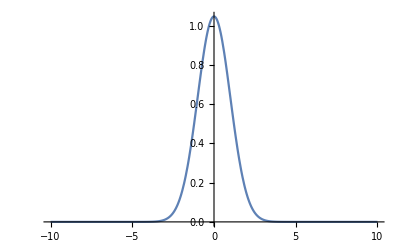

```mathematica
Plot[Sum[vecs[[1,i]]basis[[i+1]],{i,1,M}],{x,a,b},PlotRange->All]
```

Plots of the eigenfunctions are very time consuming because it involves a sum over all 50 basis functions which are themselves complicated.  This could be sped up enormously by evaluating the only at the abscissa.